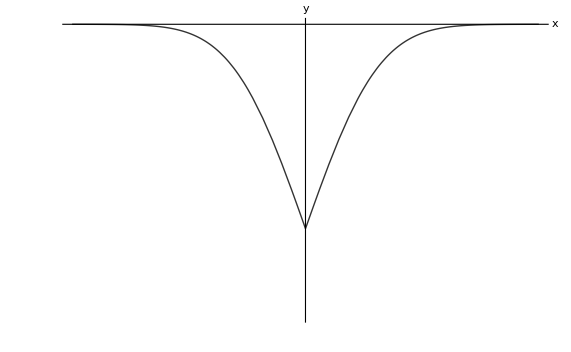

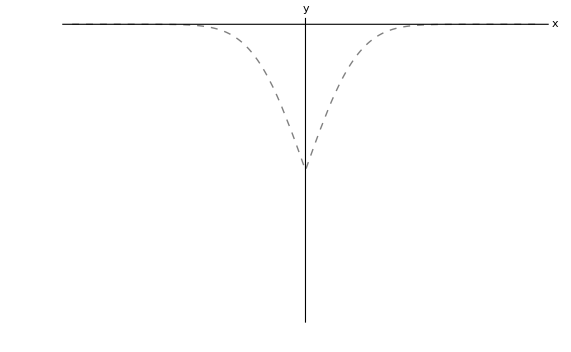

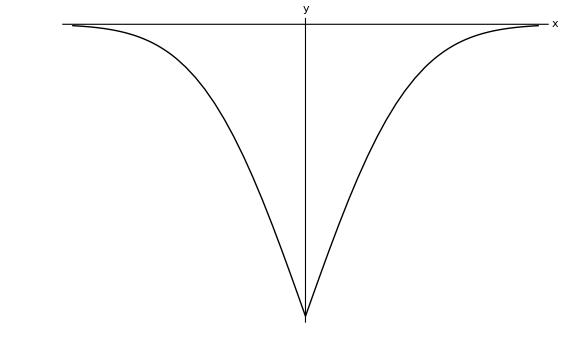

```mathematica
q=Plot[-0.7*Erfc[Abs[x/0.7]],{x,-2,2},PlotRange->{-1,0},Frame->False,AxesLabel->{x,y},PlotStyle->{GrayLevel[.2],Thick},Frame->True,GridLines->Automatic, AxesStyle->Directive[Black,22],Ticks->None]
f=Plot[-0.5*Erfc[Abs[x/0.5]],{x,-2,2},PlotRange->{-1,0},Frame->False,AxesLabel->{x,y},PlotStyle->{GrayLevel[.5],Dashed,Thick},Frame->True,GridLines->Automatic, AxesStyle->Directive[Black,22],Ticks->None]
p=Plot[-Erfc[Abs[x]],{x,-2,2},PlotRange->{-1,0},Frame->False,AxesLabel->{x,y},PlotStyle->{Black,Thick},Frame->True,GridLines->Automatic, AxesStyle->Directive[Black,22],Ticks->None]
```

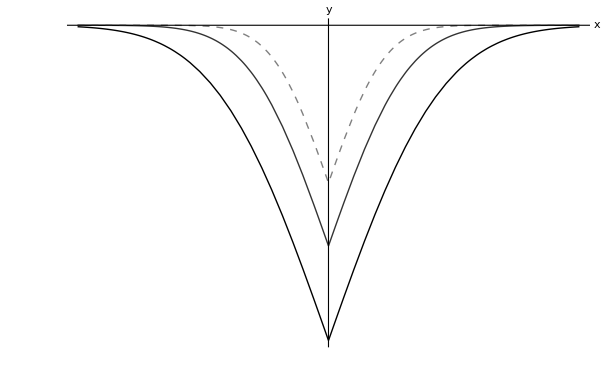

```mathematica
Show[p,q,f]
```